# Fully implicit scheme

## Fully implicit method with expanding space grid

Backward-difference (fully implicit) method with expanding grid using an expansion in x space for simulating a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals2];

makeVarDiagonals2[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]
```

```mathematica
Clear[𝔻,a,x,y,z];
{x,y,z}=makeVarDiagonals2[6,𝔻][a]
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]//MatrixForm
```

{{-𝔻/a^2,-𝔻/a^4,-𝔻/a^6},{1+((1+a) 𝔻)/a,1+((1+a) 𝔻)/a^3,1+((1+a) 𝔻)/a^5,1+((1+a) 𝔻)/a^7},{-𝔻/a,-𝔻/a^3,-𝔻/a^5}}

(1+((1+a) 𝔻)/a | -𝔻/a | 0 | 0
-𝔻/a^2 | 1+((1+a) 𝔻)/a^3 | -𝔻/a^3 | 0
0 | -𝔻/a^4 | 1+((1+a) 𝔻)/a^5 | -𝔻/a^5
0 | 0 | -𝔻/a^6 | 1+((1+a) 𝔻)/a^7)

## Set Up Solution

### LinearSolve Solution

```mathematica
Clear[implicitVarSolve];

implicitVarSolve[m_Integer,n_Integer,d_][a_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];

solveNext:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d*a^(5-2*m);
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

NestList[solveNext,initial,n-1]]
```

## Set Parameter Values

```mathematica
Clear[n,a,𝔻,tmp,m,c];

n=100;

a=1.2;

𝔻=2.;
tmp=Solve[∑_(j=1)^(m-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),m,InverseFunctions-> True];
m=1+m/.tmp⟦1⟧//Ceiling;
```

```mathematica
FindRoot[∑_(j=1)^(i-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),{i,15},MaxIterations-> 20]
```

{i→17.0652}

## Solve

LinearSolve solution

```mathematica
Clear[c];

Timing[
c=implicitVarSolve[m,n,𝔻][a];
c=Rest[c];]
```

{0.00594,Null}

#### Comparison with analytical result

```mathematica
p=60;(*enter a time increment*)

𝒟=10^-5;

time=1.;

Δt=time/(n-1)//N;
Δx=√((2*𝒟*Δt)/((1+a)*𝔻));
cb=Table[Erf[(Δx*∑_(k=1)^j a^(k-1))/(2*Sqrt[𝒟*Δt*p])]/(c⟦p,j+1⟧),{j,1,m-1}]
```

{0.99145,0.991362,0.991299,0.991291,0.991388,0.99167,0.992261,0.993318,0.994982,0.997199,0.999453,1.00079,1.00081,1.0003,1.00005,1.,1.,1.}

## Plot Current v. Time

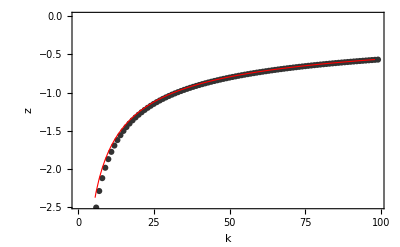

```mathematica
Clear[i,z];
i=Map[((#⟦3⟧-#⟦2⟧*(1+a)^2)*√((𝔻*(n-1))/(2*a^2*(1+a))))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}]//N;

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```